```mathematica
a=({{1, 0, 0, 0, 0, 0, 0}, {1, -((Pi^2)/72), 1, 0, 0, 0, 0}, {0, 1, -((Pi^2)/72), 1, 0, 0, 0}, {0, 0, 1, -((Pi^2)/72), 1, 0, 0}, {0, 0, 0, 1, -((Pi^2)/72), 1, 0}, {0, 0, 0, 0, 1, -((Pi^2)/72), 1}, {0, 0, 0, 0, 0, 0, 1}})
```

{{1,0,0,0,0,0,0},{1,-π^2/72,1,0,0,0,0},{0,1,-π^2/72,1,0,0,0},{0,0,1,-π^2/72,1,0,0},{0,0,0,1,-π^2/72,1,0},{0,0,0,0,1,-π^2/72,1},{0,0,0,0,0,0,1}}

```mathematica
b=({{0}, {((Pi^2)/576)*Cos[Pi/24]}, {((Pi^2)/576)*Cos[Pi/12]}, {((Pi^2)/576)*Cos[Pi/8]}, {((Pi^2)/576)*Cos[Pi/6]}, {((Pi^2)/576)*Cos[(5*Pi)/24]}, {0}})
```

{{0},{1/576 π^2 Cos[π/24]},{((1+√3) π^2)/(1152 √2)},{1/576 π^2 Cos[π/8]},{π^2/(384 √3)},{1/576 π^2 Cos[(5 π)/24]},{0}}

```mathematica
LinearSolve[a,b]
```

{{0},{(186624 √2 π^2-186624 √3 π^2+186624 √6 π^2-18 √2 π^6-18 √6 π^6-26873856 Cos[π/24]+15552 π^4 Cos[π/24]-π^8 Cos[π/24]+26873856 Cos[π/8]-5184 π^4 Cos[π/8]-26873856 Cos[(5 π)/24])/(8 (80621568-20736 π^4+π^8))},{(10368 √2 π^4-10368 √3 π^4+10368 √6 π^4-√2 π^8-√6 π^8+2985984 π^2 Cos[π/24]-288 π^6 Cos[π/24]+1492992 π^2 Cos[π/8]-288 π^6 Cos[π/8]-1492992 π^2 Cos[(5 π)/24])/(32 (80621568-20736 π^4+π^8))},{(-18 √2 π^2-36 √3 π^2-18 √6 π^2-5184 Cos[π/24]+5184 Cos[π/8]-π^4 Cos[π/8]-5184 Cos[(5 π)/24])/(8 (-15552+π^4))},{(-2592 √2 π^4+10368 √3 π^4-2592 √6 π^4-√3 π^8-746496 π^2 Cos[π/24]+746496 π^2 Cos[π/8]-144 π^6 Cos[π/8]+1492992 π^2 Cos[(5 π)/24]-144 π^6 Cos[(5 π)/24])/(16 (80621568-20736 π^4+π^8))},{(-93312 √2 π^2+373248 √3 π^2-93312 √6 π^2-36 √3 π^6-26873856 Cos[π/24]+26873856 Cos[π/8]-5184 π^4 Cos[π/8]-26873856 Cos[(5 π)/24]+15552 π^4 Cos[(5 π)/24]-π^8 Cos[(5 π)/24])/(8 (80621568-20736 π^4+π^8))},{0}}

```mathematica
{(186624 √2 π^2-186624 √3 π^2+186624 √6 π^2-18 √2 π^6-18 √6 π^6-26873856 Cos[π/24]+15552 π^4 Cos[π/24]-π^8 Cos[π/24]+26873856 Cos[π/8]-5184 π^4 Cos[π/8]-26873856 Cos[(5 π)/24])/(8 (80621568-20736 π^4+π^8))}//N
```

{-0.0290206}

```mathematica
{(10368 √2 π^4-10368 √3 π^4+10368 √6 π^4-√2 π^8-√6 π^8+2985984 π^2 Cos[π/24]-288 π^6 Cos[π/24]+1492992 π^2 Cos[π/8]-288 π^6 Cos[π/8]-1492992 π^2 Cos[(5 π)/24])/(32 (80621568-20736 π^4+π^8))}//N
```

{0.0130101}

```mathematica
{1/(8 (-15552+π^4))(-18 √2 π^2-36 √3 π^2-18 √6 π^2-5184 Cos[π/24]+5184 Cos[π/8]-π^4 Cos[π/8]-5184 Cos[(5 π)/24])}//N
```

{0.0473549}

```mathematica
{(-2592 √2 π^4+10368 √3 π^4-2592 √6 π^4-√3 π^8-746496 π^2 Cos[π/24]+746496 π^2 Cos[π/8]-144 π^6 Cos[π/8]+1492992 π^2 Cos[(5 π)/24]-144 π^6 Cos[(5 π)/24])/(16 (80621568-20736 π^4+π^8))}//N
```

{0.00931167}

```mathematica
{(-93312 √2 π^2+373248 √3 π^2-93312 √6 π^2-36 √3 π^6-26873856 Cos[π/24]+26873856 Cos[π/8]-5184 π^4 Cos[π/8]-26873856 Cos[(5 π)/24]+15552 π^4 Cos[(5 π)/24]-π^8 Cos[(5 π)/24])/(8 (80621568-20736 π^4+π^8))}//N
```

{-0.0312393}

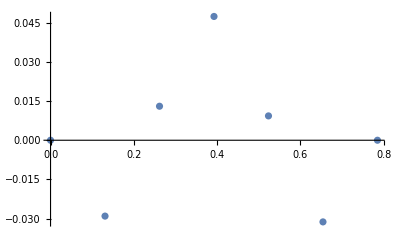

```mathematica
ListPlot[{{0,0},{Pi/24,-0.029020610595483852},{Pi/12,0.013010057289598064},{Pi/8,0.047354879233919955},{Pi/6,0.009311673432886285},{(5*Pi)/24,-0.03123934381481604},{Pi/4,0}}]
```